# CRMSD and D

## data loading

```mathematica
p0s={3.9,3.85,3.825,3.80,3.775,3.75};
```

```mathematica
temperatures={{0.039,0.01,0.005,0.002,0.001,0.0005,0.00033,0.00014,0.000091,0.000077,0.000054,0.000045,0.000036},{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.03105, 0.025 ,0.02 ,0.016 ,0.012, 0.01, 0.009 ,0.008 ,0.0075, 0.007 ,0.0063, 0.0056 ,0.0054},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{10, 19, 9,9,46.2416,35.0693,135.321,564.239,829.48,897.484,1365.27,1522.57,3000},{2, 4,10, 20, 40,60, 80, 200, 500, 800, 1400, 2500, 4200,5000, 6000, 8500, 9500},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{1, 3, 4 ,8 ,15,40 ,70 ,150 ,250, 600 ,2000, 2500 ,4500, 9500},{2, 10,20 ,30, 80 ,100 ,400 ,500 ,2500 ,2500, 3000 ,7000, 10000},{4 ,5 ,7 ,10 ,30 ,70, 150 ,700,1400, 4000 ,9500}};
```

```mathematica
orientationals=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/orientationReIm_N4096_p","_T","_",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],records[[p,i]]},{3,3,8,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
orientationalsReal[[2,14]]
```

Table[DeleteCases[Table[orientationals⟦p,T,i,1,rec⟧,{i,Length[orientationals⟦p,T⟧]}],_Missing|_Part],{rec,-∞}]

```mathematica
translationals=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/translationReIm_N4096_p","_T","_",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],records[[p,i]]},{3,3,8,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
Normal[sigmaXXsigmaYYs[[1,1,1,1]]]
```

{0.251468,0.244393,0.247302,0.238019,0.246261,0.247319,0.239919,0.244294,0.243343,0.242202,0.242348}

```mathematica
Flatten[{{{1,2},2,{{2,1}}}}]
```

{1,2,2,2,1}

```mathematica
orientationals[[2,14]]
```

{}

```mathematica
Table[Table[Table[Length[orientationals[[p,T,i,1]]],{i,Length[orientationals[[p,T]]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{{11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,11,11,11,11},{11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11}},{{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,10,11,10,11},{11,11,11,11,11,11,8,11,11,11}},{{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{3,5,5,3,1,4,4,4,3,3},{2,3,3,3,3,1,2,1,1,1}},{{11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,7,8,11,11,11,11,11},{11,5,11,4,4,10,9},{4,5,4,5,1,5,5,1},{1,2,3,2,2,2,2,3}},{{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11}},{{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{1,2,5,1,5,5,1,6},{2,2,2,2,2,3,2}}}

```mathematica
orientationalsReal=Table[Table[Flatten[Table[DeleteCases[Table[orientationals[[p,T,i,1,rec]],{i,Length[orientationals[[p,T]]]}],_Missing|_Part],{rec,Max[Table[Length[orientationals[[p,T,i,1]]],{i,Length[orientationals[[p,T]]]}]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 11 of … does not exist.

Part::partw: Part 9 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
orientationalsIm=Table[Table[Flatten[Table[DeleteCases[Table[orientationals[[p,T,i,2,rec]],{i,Length[orientationals[[p,T]]]}],_Missing|_Part],{rec,Max[Table[Length[orientationals[[p,T,i,1]]],{i,Length[orientationals[[p,T]]]}]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 11 of … does not exist.

Part::partw: Part 9 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
VarOri=Table[Table[Variance[Table[Sqrt[orientationalsIm[[p,T,rec]]^2+orientationalsReal[[p,T,rec]]^2],{rec,Length[orientationalsIm[[p,T]]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
VarOri
```

{{0.000024906,0.0000237851,0.0000249544,0.0000263616,0.0000330017,0.0000222213,0.0000253206,0.0000260771,0.0000233739,0.0000260104,0.0000220208,0.0000245192,0.0000239637},{0.0000301701,0.0000468281,0.0000683461,0.0000599482,0.000091052,0.000100472,0.00012323,0.000110957,0.000118597,0.000113957,0.000124039,0.000118636,0.000142498,0.000134309,0.000182314,0.000124635,0.000251869},{0.0000249455,0.0000340848,0.00005006,0.0000590883,0.0000949429,0.000120529,0.000183249,0.000227236,0.00025026,0.000362483,0.000466289,0.000504535,0.00105208,0.00270169,0.00297227,0.000608696},{0.0000410703,0.0000389916,0.0000561167,0.0000769108,0.000109169,0.000241223,0.000442681,0.00084194,0.00225557,0.0048254,0.0015261,0.000614719,0.000197638,0.000118758},{0.0000790313,0.000118981,0.000143367,0.000284167,0.000816288,0.00249779,0.00385576,0.00166658,0.00172543,0.000685225,0.00019879,0.000115117,0.000087578},{0.0000423592,0.0000739827,0.000118068,0.000157976,0.000388524,0.000872396,0.0038062,0.00134818,0.000352668,0.000195169,0.0000490992}}

```mathematica
VarOri
```

{{0.0000301701,0.0000468281,0.0000683461,0.0000599482,0.000091052,0.000100472,0.00012323,0.000110957,0.000118597,0.000113957,0.000124039,0.000118636,0.000142498,0.000134309,0.000182314,0.000124635,0.000251869},{0.0000249455,0.0000340848,0.00005006,0.0000590883,0.0000949429,0.000120529,0.000183249,0.000227236,0.00025026,0.000362483,0.000466289,0.000504535,0.00105208,0.00270169,0.00297227,0.000608696},{0.0000410703,0.0000389916,0.0000561167,0.0000769108,0.000109169,0.000241223,0.000442681,0.00084194,0.00225557,0.0048254,0.0015261,0.000614719,0.000197638,0.000118758},{0.0000790313,0.000118981,0.000143367,0.000284167,0.000816288,0.00249779,0.00385576,0.00166658,0.00172543,0.000685225,0.00019879,0.000115117,0.000087578},{0.0000423592,0.0000739827,0.000118068,0.000157976,0.000388524,0.000872396,0.0038062,0.00134818,0.000352668,0.000195169,0.0000490992}}

```mathematica
translationalReal=Table[Table[Flatten[Table[DeleteCases[Table[translationals[[p,T,i,1,rec]],{i,Length[translationals[[p,T]]]}],_Missing|_Part],{rec,Max[Table[Length[translationals[[p,T,i,1]]],{i,Length[translationals[[p,T]]]}]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 11 of … does not exist.

Part::partw: Part 9 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
translationalIm=Table[Table[Flatten[Table[DeleteCases[Table[translationals[[p,T,i,2,rec]],{i,Length[translationals[[p,T]]]}],_Missing|_Part],{rec,Max[Table[Length[translationals[[p,T,i,1]]],{i,Length[translationals[[p,T]]]}]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 11 of … does not exist.

Part::partw: Part 9 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
VarTrans=Table[Table[Variance[Table[Sqrt[translationalIm[[p,T,rec]]^2+translationalReal[[p,T,rec]]^2],{rec,Length[orientationalsIm[[p,T]]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
VarTrans
```

{{0.0000514885,0.0000723372,0.0000998845,0.000118544,0.00010094,0.00011182,0.000107955,0.000120259,0.000140906,0.000119204,0.000111151,0.000154206,0.000171507,0.000095929,0.000115839,0.000150025,0.000128151},{0.0000740906,0.0000910399,0.0000833416,0.000118127,0.00011846,0.000127165,0.000122982,0.000116032,0.000136256,0.000137062,0.000128482,0.000124591,0.000127215,0.000162129,0.000111069,0.000711172},{0.0000722533,0.0000800723,0.000118029,0.0000816652,0.000100038,0.000158919,0.00016646,0.000161923,0.000205021,0.000198996,0.000425862,0.00012176,0.000889531,0.000339863},{0.000102714,0.000112271,0.000114196,0.000124635,0.000165866,0.000200528,0.000187505,0.000298548,0.00065653,0.000673561,0.00178496,0.0013694,0.00273007},{0.0000759618,0.0000924791,0.0000999969,0.000100554,0.000155772,0.000192148,0.000292931,0.000870244,0.000104221,0.000473715,0.000122538}}

```mathematica
χ
```

## Plots and fitting

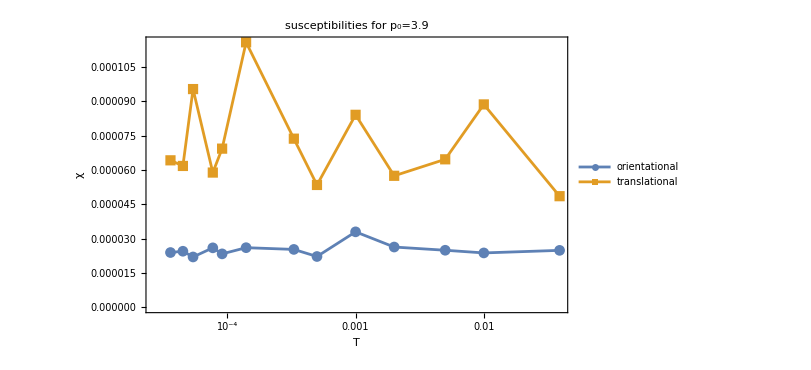
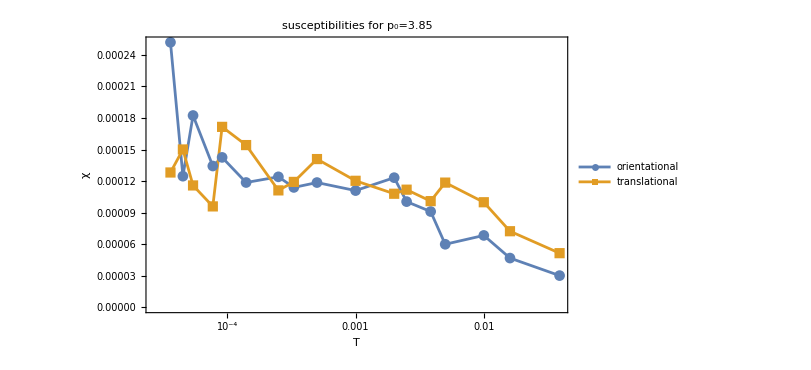
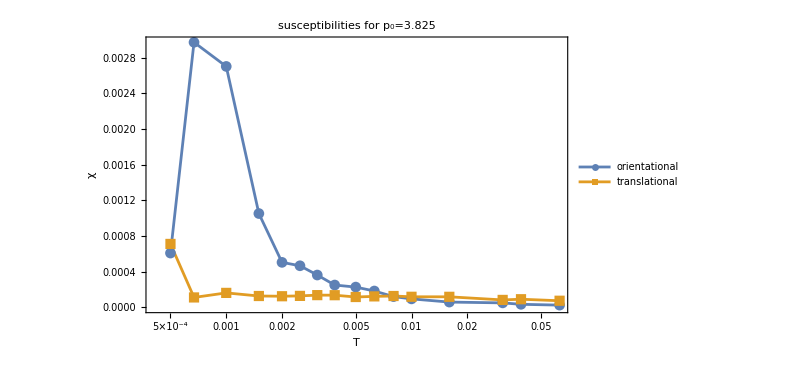
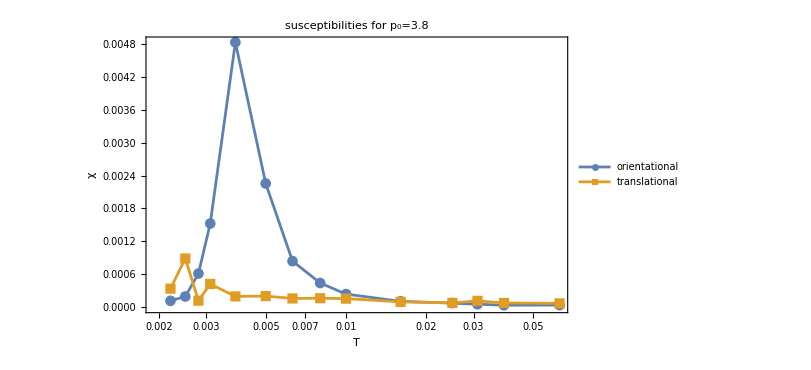
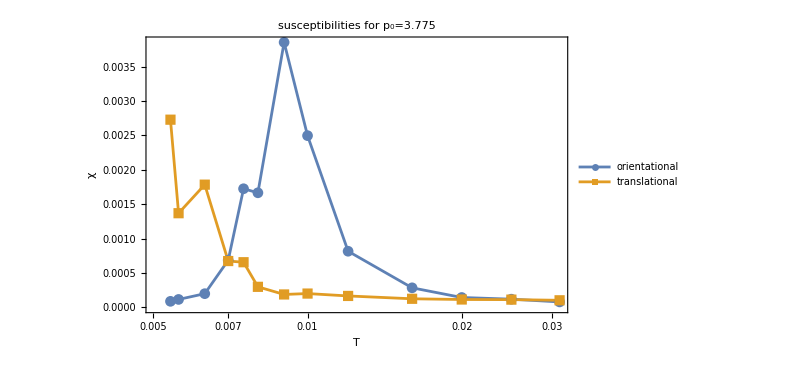
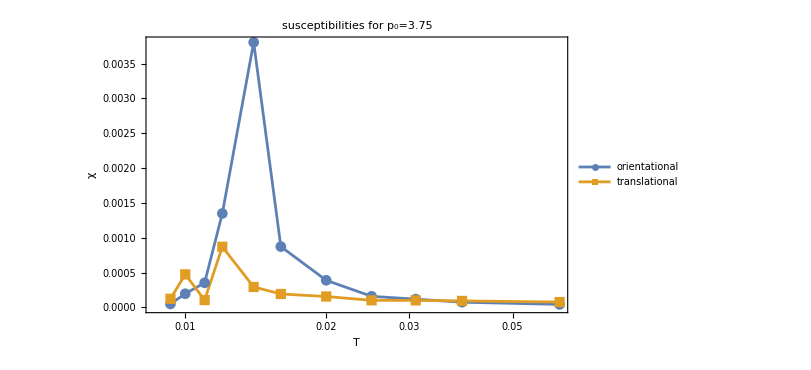

```mathematica
orderparameter=Table[ListLogLinearPlot[{Table[{temperatures[[p,T]],VarOri[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],VarTrans[[p,T]]},{T,Length[temperatures[[p]]]}]},PlotLegends->{"orientational","translational"},PlotStyle->Automatic,FrameLabel->{"T","χ"},ImageSize->600,PlotLabel->"susceptibilities for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->All,PlotMarkers->Automatic],{p,Length[p0s]}]
```

```mathematica
Table[Export["/home/chengling/Research/updates/04112024/orderPa"<>ToString[p0s[[p]]]<>".jpeg",orderparameter[[p]],ImageResolution->600],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/04112024/orderPa3.85.jpeg,/home/chengling/Research/updates/04112024/orderPa3.825.jpeg,/home/chengling/Research/updates/04112024/orderPa3.8.jpeg,/home/chengling/Research/updates/04112024/orderPa3.775.jpeg,/home/chengling/Research/updates/04112024/orderPa3.75.jpeg}